# LHW 11: Solution

Make a Julia notebook or Mathematica notebook computing the least square fit of a 7th degree polynomial
	atan(1+3 sin(x)+cos^2(3x)+ln(1+x^2))
using m equally spaced points on the interval [-1,1].  Do not use a black box solver. Assume m>8 and explain the linear algebra you are doing to solve your system.

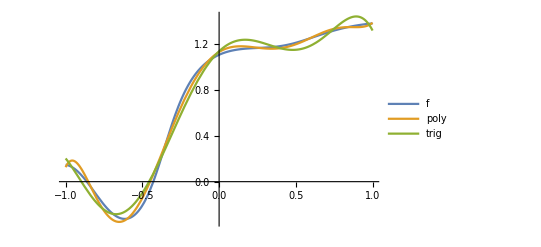

```mathematica
ps[x_]:={1,x,x^2,x^3,x^4,x^5,x^6,x^7}
ts[x_]:={1, Cos[x],Cos[2x],Cos[3x],Sin[x],Sin[2x],Sin[3x]}
f[x_]:= ArcTan[1 + 3 Sin[x]+Cos[3x]^2+Log[1+x^2]]
m=23;{a,b}={-1.0,1};
xs= Range[a,b,(b-a)/(m-1)];
fs = f[xs];
Ap=Map[ps,xs];
At=Map[ts,xs];
(* Built in Black Box Solver *)
apLS =LeastSquares[Ap,fs];
atLS =LeastSquares[At,fs];
Plot[ {f[x],apLS.ps[x], atLS.ts[x]},{x,a,b},
PlotLegends->{"f","poly","trig"}]
```

Doing different linear algebra for polynomials fit.

```mathematica
(* Normal Equations Projection *)
apNorm =LinearSolve[Apᵀ.Ap,Apᵀ.fs];
(* SVD *)
{U,S,V}=SingularValueDecomposition[Ap,8];
apSVD = V.Inverse[S].Uᵀ.fs;
(* QR remember Mathematica gives out Q on its side! *)
{Qpt,Rp}=QRDecomposition[Ap];
apQR = LinearSolve[Rp,Qpt.fs];
(* Pseudo Inverse *)
apPInv = PseudoInverse[Ap].fs;
Map[ Norm,{apNorm-apLS,apNorm-apLS,apNorm-apLS,apNorm-apLS,apQR-apLS}]
```

{5.1604×10^-12,5.1604×10^-12,5.1604×10^-12,5.1604×10^-12,2.9031×10^-14}